```mathematica
(*Question 5*)
f = {2,1,-3,2,1};
filter = {1,0,-1};
ListConvolve[Reverse@filter,f]
```

{5,-1,-4}

```mathematica
(*Question 4*)
sigmoid[x_]:=1/(1+ⅇ^-x);
relu[x_]:=Max[x,0];
Manipulate[Plot[sigmoid[w*relu[u*x+b]+v],{x,0,10}],{w,-5,5},{u,-5,5},{b,-5,5},{v,-5,5}]
```

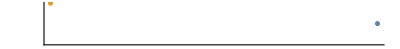

```mathematica
(*Question 3*)
Clear[pos,neg,f];
pos = Table[π*2i,{i,1,5}];
neg = Table[π*(2i-1),{i,1,5}];
f[x_]:=Cos[x];
NumberLinePlot[{f/@pos,f/@neg},PlotTheme->"Minimal"]
```

```mathematica
Clear[α,a,b,c,d,e,f,g,h,m,n,x,y];
x=Table[π*i,{i,10}];
y= Table[(-1)^i,{i,1,10}];
α ={1,1,1,1,1,1,1,1,1,1};
k[x_,y_]:=Exp[-10*(x-y)^2];
AllTrue[Table[y⟦i⟧*Sum[α⟦j⟧*y⟦j⟧*k[x⟦i⟧, x⟦j⟧],{j,1,10}]>0,{i,1,10}],TrueQ[#]&]
```

True

```mathematica
(*Question 6*)
```

```mathematica
Maximize[{(Subscript[θ, A])^3*(1-Subscript[θ, A])*(Subscript[θ, B])^2*(1-Subscript[θ, B])^2,0<Subscript[θ, A]<1,0<Subscript[θ, B]<1},{Subscript[θ, A],Subscript[θ, B]}]
```

{27/4096,{θ_A→3/4,θ_B→1/2}}

```mathematica
Flatten[{27/4096,{Subscript[θ, A]->3/4,Subscript[θ, B]->1/2}}]
```

{27/4096,θ_A→3/4,θ_B→1/2}

```mathematica
12.48+16*1/(2.5+7+2+7+4)
```

13.1911

```mathematica
Subscript[θ, A]=0.6;
Subscript[θ, B]=0.4;
((Subscript[θ, A])^3*(1-Subscript[θ, A])^1)/((Subscript[θ, A])^3*(1-Subscript[θ, A])^1+(Subscript[θ, B])^3*(1-Subscript[θ, B])^1)
```

0.692308

```mathematica
Rationalize[0.6923076923076922]
```

9/13

```mathematica
Maximize[{1/2 Log[1/2*(Subscript[θ, A])^2*(1-Subscript[θ, A])^2]+1/2 Log[1/2*(Subscript[θ, B])^2*(1-Subscript[θ, B])^2]
+9/13 Log[9/13*(Subscript[θ, A])^3*(1-Subscript[θ, A])^1]+4/13 Log[4/13*(Subscript[θ, B])^3*(1-Subscript[θ, B])^1]
,0<Subscript[θ, A]<1,0<Subscript[θ, B]<1},{Subscript[θ, A],Subscript[θ, B]}]
```

Maximize::ivar: 0.6 is not a valid variable.

Maximize[{-6.86291,True,True},{0.6,0.4}]